# UT Physics Fire Truck Problem

## Analysis

## Initialization

## Clear Up

```mathematica
(*Clear any previously defined symbols*)
ClearAll["Global`*"];
```

## Parameters

### Truck Parameters

-Graphics-
sizes are in mm.

```mathematica
mass = 30000;
truckHeight = 3.7;
wheelBase = 3.825;
```

## Road Profile

We’ll assume a slope of angle  and a bump on it with the function:
 where  is the max height of the bump  makes the deviation (lower bump at the edges of the bump. This function only applies where the bump is so if  we should set it to zero.

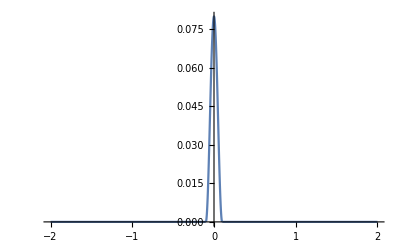

```mathematica
maxHeight=0.08;
deviation=0.1;
bumpProfile[x_]:=Piecewise[{{maxHeight/2 (1+Cos[Pi x/deviation]),Abs[x]<=deviation},{0,Abs[x]>deviation}}];
Plot[bumpProfile[x],{x,-2,2}]
```

Now the slope can be modeled easily by:
.

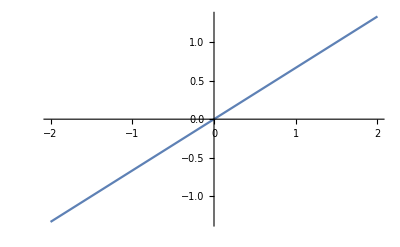

```mathematica
slopeAngle = Pi/4;
slopeProfile[x_]:=x ArcTan[slopeAngle];
Plot[slopeProfile[x],{x,-2,2}]
```

Putting them together:

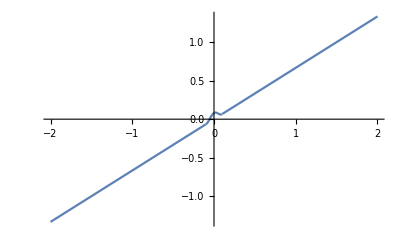

```mathematica
roadProfile[x_]:=slopeProfile[x]+bumpProfile[x];
Plot[roadProfile[x],{x,-2,2}]
```

## Modeling the Truck

## Rigid Body

We consider the truck as a rigid body and not consider the pressure of the tires that would cause the truck to jump in the incidence of hitting the bump fast. Let’s also assume the truck’s wheels always “hug” the road. We define:

 as the -coordinate where the rear axle contacts the road.
With a wheelbase , the front axle contacts at . Thus contact points are:

```mathematica
rearContactPoint={xr, roadProfile[xr]}
frontContactPoint={xr+wheelBase, roadProfile[xr+wheelBase]}
```

{xr,xr ArcTan[π/4]+(Piecewise[{{0.04 (1+Cos[31.4159 xr]), Abs[xr]≤0.1}, {0, True}}])}

{3.825+xr,(3.825+xr) ArcTan[π/4]+(Piecewise[{{0.04 (1+Cos[31.4159 (3.825+xr)]), Abs[3.825+xr]≤0.1}, {0, True}}])}

The line joining the two axles has slope:

```mathematica
slopeOfTruck = (roadProfile[xr+wheelBase]-roadProfile[xr])/wheelBase
```

0.261438 (-xr ArcTan[π/4]+(3.825+xr) ArcTan[π/4]-(Piecewise[{{0.04 (1+Cos[31.4159 xr]), Abs[xr]≤0.1}, {0, True}}])+(Piecewise[{{0.04 (1+Cos[31.4159 (3.825+xr)]), Abs[3.825+xr]≤0.1}, {0, True}}]))

Thus the angle of this line with the horizontal line is:

```mathematica
truckAngle=ArcTan[slopeOfTruck]
```

ArcTan[0.261438 (-xr ArcTan[π/4]+(3.825+xr) ArcTan[π/4]-(Piecewise[{{0.04 (1+Cos[31.4159 xr]), Abs[xr]≤0.1}, {0, True}}])+(Piecewise[{{0.04 (1+Cos[31.4159 (3.825+xr)]), Abs[3.825+xr]≤0.1}, {0, True}}]))]

Assume the highest point of the truck (its “roof”) is located a fixed distance  perpendicular to the axle line when the truck is level (this  is essentially the excess height of the truck’s roof above the axles). In the truck’s frame this is constant, but relative to the ground the vertical component changes with the truck’s rotation.

The midpoint of the axle line is:

```mathematica
midpointOfAxleLine={xr+wheelBase/2,(roadProfile[xr]+roadProfile[xr+wheelBase])/2}
```

{1.9125+xr,1/2 (xr ArcTan[π/4]+(3.825+xr) ArcTan[π/4]+(Piecewise[{{0.04 (1+Cos[31.4159 xr]), Abs[xr]≤0.1}, {0, True}}])+(Piecewise[{{0.04 (1+Cos[31.4159 (3.825+xr)]), Abs[3.825+xr]≤0.1}, {0, True}}]))}

When the chassis rotates by , the vertical offset of the roof above this midpoint is . Thus, the roof’s vertical coordinate relative to the ground is approximately:

```mathematica
roofHeightCoordinate[xr_]:=(roadProfile[xr]+roadProfile[xr+wheelBase])/2+ truckHeight Cos[ArcTan[(roadProfile[xr+wheelBase]-roadProfile[xr])/wheelBase]]
```

This formula gives you the roof height as a function of the truck' s position relative to the bump.

## Considering Speed and Jump

## Evaluation of the Worst-Case Clearance

## Static Clearance

For the truck to clear the topbar, topbar height must be at least the maximum value of the roof height function.